```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
data=Import["data_with_time_windows2.mx"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
Dimensions@DeleteDuplicates@data[[1]][[All,9]]
```

{80}

Width Feature

```mathematica
window=1;
rawaim=data[[window]][[All,9]];
pos=Partition[Flatten@Table[Position[rawaim,i],{i,{"NA",0}}],1];
aim=Delete[rawaim,pos];
campaign=Delete[data[[window]][[All,2]],pos];
seri=Delete[data[[window]][[All,1]],pos];
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {78}

aim data length: {40209}

sequence data groups amount: {122}

```mathematica
Print["bucket size: ",bucketsize=Ceiling@(N@(Dimensions@aim)/55)]
aimlabeled=Thread[Range@Length@aim->aim];
aimpartitioned=Partition[Normal@Sort@Association@aimlabeled,UpTo@bucketsize];
bins=Table[MinMax[i],{i,Values@aimpartitioned}];
Print["node amount: ",Length@bins];
```

bucket size: {732}

node amount: 55

```mathematica
repetitivesreport=DeleteCases[Tally@bins,x_/;x[[2]]==1];
repetitives=repetitivesreport[[All,1]];
labelgeneration[x_]:=Table[{repetitives[[x]][[1]]+i*repetitives[[x]][[1]]/10^(RealDigits@repetitives[[x]][[1]])[[2]],repetitives[[x]][[2]]+i*repetitives[[x]][[2]]/10^(RealDigits@repetitives[[x]][[2]])[[2]]},{i,Range@repetitivesreport[[x]][[2]]}]
binsrearranged=ReplacePart[bins,Flatten[Table[MapThread[#1->#2&,{Flatten@Position[bins,repetitives[[g]]],labelgeneration[g]}],{g,Range@Length@repetitives}],1]];
```

```mathematica
aimbinned=Values@Normal@KeySort@Association@Flatten[Table[aimpartitioned[[i]]/.Table[Values@aimpartitioned[[i]][[j]]->binsrearranged[[i]],{j,Length@aimpartitioned[[i]]}],{i,Length@aimpartitioned}],1];
Position[aimbinned,Null]
```

{}

```mathematica
aim=aimbinned;
binningmembers=Sort[DeleteDuplicates[aim]];
Print["binning amount: ",Dimensions@DeleteDuplicates@aimbinned]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

binning amount: {55,2}

dimension of binned data: {40209,2}

binning members dimension : {55,2}

```mathematica
binningmembers=Sort[DeleteDuplicates[aim]]
```

{{1060.,1180.},{1180.,1220.},{1220.,1230.},{1220.12,1220.12},{1220.24,1220.24},{1220.37,1220.37},{1220.49,1220.49},{1220.61,1220.61},{1230.,1240.},{1230.12,1230.12},{1230.25,1230.25},{1230.37,1230.37},{1240.,1240.},{1240.,1250.},{1250.,1270.},{1270.,1320.},{1320.,1350.},{1350.,1390.},{1390.,1400.},{1400.,1460.},{1460.,1480.},{1480.,1510.},{1510.,1510.},{1510.,1520.},{1520.,1530.},{1530.,1540.},{1530.15,1530.15},{1530.31,1530.31},{1530.46,1530.46},{1530.61,1530.61},{1530.77,1530.77},{1530.92,1530.92},{1531.07,1531.07},{1531.22,1531.22},{1540.,1550.},{1540.15,1540.15},{1540.31,1540.31},{1540.46,1540.46},{1540.62,1540.62},{1550.,1580.},{1580.,1600.},{1600.,1620.},{1620.,1670.},{1670.,1800.},{1800.,1840.},{1840.,1850.},{1840.18,1840.18},{1840.37,1840.37},{1840.55,1840.55},{1840.74,1840.74},{1850.,1860.},{1850.19,1850.19},{1850.37,1850.37},{1850.56,1850.56},{1860.,1880.}}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

binning groups association to count of their total members: <|{1060.,1180.}→732,{1180.,1220.}→732,{1220.,1230.}→732,{1220.12,1220.12}→732,{1220.24,1220.24}→732,{1220.37,1220.37}→732,{1220.49,1220.49}→732,{1220.61,1220.61}→732,{1230.,1240.}→732,{1230.12,1230.12}→732,{1230.25,1230.25}→732,{1230.37,1230.37}→732,{1240.,1240.}→732,{1240.,1250.}→732,{1250.,1270.}→732,{1270.,1320.}→732,{1320.,1350.}→732,{1350.,1390.}→732,{1390.,1400.}→732,{1400.,1460.}→732,{1460.,1480.}→732,{1480.,1510.}→732,{1510.,1510.}→732,{1510.,1520.}→732,{1520.,1530.}→732,{1530.,1540.}→732,{1530.15,1530.15}→732,{1530.31,1530.31}→732,{1530.46,1530.46}→732,{1530.61,1530.61}→732,{1530.77,1530.77}→732,{1530.92,1530.92}→732,{1531.07,1531.07}→732,{1531.22,1531.22}→732,{1540.,1550.}→732,{1540.15,1540.15}→732,{1540.31,1540.31}→732,{1540.46,1540.46}→732,{1540.62,1540.62}→732,{1550.,1580.}→732,{1580.,1600.}→732,{1600.,1620.}→732,{1620.,1670.}→732,{1670.,1800.}→732,{1800.,1840.}→732,{1840.,1850.}→732,{1840.18,1840.18}→732,{1840.37,1840.37}→732,{1840.55,1840.55}→732,{1840.74,1840.74}→732,{1850.,1860.}→732,{1850.19,1850.19}→732,{1850.37,1850.37}→732,{1850.56,1850.56}→732,{1860.,1880.}→681|>

binning amount: {55,2}

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.0134852,Null}

{55,2}

{1485,2,2}

{122}

{1.18752,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

{0.0174263,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

{511,2,2}

{0.121825,Null}

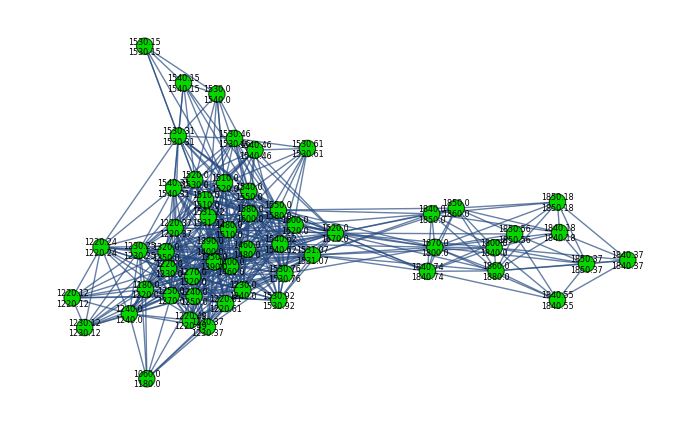

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->1,VertexStyle->RGBColor[0.02,0.84,0.],VertexLabelStyle->Directive[Black,Italic,8],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->700]
```